Links to all notebooks

basicsDMDO
calc1 calc2 calc3 calc4 calc5
matrices
ode
odesys

# (Ordinary) Differential Equations (ODE)

```mathematica
DSolve, NDSolve, VectorPlot
```

## Linear First Order Differential Equation (FODE)

This notebook is about solving and analyzing one single differential equation. For solving systems of two differential equations see the notebooks odesys1.nb to odesys4.nb. 
If we encounter a differential equation, then we first try to solve it exactly. For this the command DSolve can be used. Solutions will be explicit functions (of time t), sometimes called symbolic or algebraic solutions, which may contain parameters, like undetermined intial values.
However, in many cases exact solutions cannot be found. Then we have to approximate a specific solution, starting at a prespecified intial point and with no other parameters in it. This can be done by the command NDSolve. The (numerical) approximation we find is not an explicit function, but some rule that will calculate for each value of time t the corresponding values of the dynamic variable(s). The only way to get an idea of the solution is to evaluate tables with function values and make plots.

## Exact solutions with DSolve

### General solutions (no initial condition)

#### Example 1 (general linear FODE with constant coefficients)

Consider the general linear First Order Differential Equation (FODE) 
	x'+a x=b 
and give it a name for easy reference, equex1 say. Always think of putting the argument, or independent time variable t, behind the (dependent) dynamic variable, between square brackets. So here, put t behind x and x'.
Besides, don't forget to put a space or an asterisk between a and x, as a multiplication command.

```mathematica
equex1=x'[t]+a x[t]==b
```

a x[t]+x'[t]==b

The built-in command "DSolve" tries to solve a differential equation in a symbolic or algebraic way.

```mathematica
?DSolve
```

```mathematica
DSolve[x'[t]+a x[t]==b,x[t],t]
```

{{x[t]→b/a+ⅇ^(-a t) C[1]}}

Note: you will observe C[1] in your answer. This is a so-called integration constant. Solving a differential equations is closely related to integration, and, as you know, an integral is not unique, but has an undetermined constant.

Of course you can use the name of the equation if it has one. Besides, you can give the solution a name, solex1 say.

```mathematica
solex1=DSolve[equex1,x[t],t]
```

{{x[t]→b/a+ⅇ^(-a t) C[1]}}

If you want to check whether you have found the right solutions, substitute the generated solutions back into the original differential equation. Here you can easily use the Mathematica replacement command "/.". The next expression means: substitute each assignment, contained in "solex1", into "equex1".

```mathematica
equex1/.solex1
```

{a (b/a+ⅇ^(-a t) C[1])+x'[t]==b}

However, as you see, the derivative of the solution solex1 is not calculated. This is because Mathematica does not recognize the solution as a (pure) function x(t) with argument t, but as an expression called x[t]. Hence the derivative of x[t] is not defined, and thus considered as a new  name. So the operation generates only a plain substitution for x[t].

One way to handle this problem is to define the derivative "solex1' " ourselves, although this is not a nice way.

```mathematica
solex1'=D[solex1, t]
```

{{x'[t]→-a ⅇ^(-a t) C[1]}}

Now the check can be executed by making substitutions for both solex1 and solex1'.

```mathematica
equex1/.solex1/. solex1'
```

{{-a ⅇ^(-a t) C[1]+a (b/a+ⅇ^(-a t) C[1])==b}}

```mathematica
Simplify[%]
```

{{True}}

Another way to check the validity of a solution is to first define a function representing the found solution.
See for this much more elegant way a next subsection on pure functions.

#### Question 1

(a) Evaluate solutions for different values of a and b in example 1. Notice, that it may be useful to define "equex1" in the delayed way, so use ": =" instead of "=".
(b) Make a table of solutions for different values of a and b in example 1, using the "Table"-command.

```mathematica
?RandomInteger
equex1:=x'[t]+RandomInteger[0,100] x[t]==RandomInteger[0,100]
solex1=DSolve[equex1,x[t],t]
```

{{x[t]→b+ⅇ^-t C[1]}}

```mathematica
{{x[t]->b/a+ⅇ^(-a t) C[1]}}
Table[DSolve[equex1,x[t],t],10]
```

{{x[t]→b/a+ⅇ^(-a t) C[1]}}

{{{x[t]→b t+C[1]}},{{x[t]→b+ⅇ^-t C[1]}},{{x[t]→b+ⅇ^-t C[1]}},{{x[t]→b+ⅇ^-t C[1]}},{{x[t]→b t+C[1]}},{{x[t]→b t+C[1]}},{{x[t]→b t+C[1]}},{{x[t]→b+ⅇ^-t C[1]}},{{x[t]→b t+C[1]}},{{x[t]→b t+C[1]}}}

#### Example 2 (variable coefficients)

Consider the equation
x' + 2tx = 5t

```mathematica
equex2=x'[t]+2 t x[t]==b t
```

2 t x[t]+x'[t]==b t

```mathematica
DSolve[equex2,x[t],t]
```

{{x[t]→b/2+ⅇ^(-t^2) C[1]}}

```mathematica
{{x[t]->ⅇ^(-t^2) C[1]+1/2 bt ⅇ^(-t^2) √π Erfi[t]}}
?Erfi
```

#### Question 2

Evaluate solutions of the equation in example 2 with righthandside bt instead of 5t.

### Adding an initial condition

By adding an initial condition, which is in fact another equation,  you will find exactly one solution.

#### Example 3

Add the initial condition x(0) = 1 to the equation in example 2.

```mathematica
solex3=DSolve[{equex2,x[0]==1},x[t],t]
```

{{x[t]→1/2 ⅇ^(-t^2) (2-b+b ⅇ^(t^2))}}

```mathematica
{{x[t]->1/2 ⅇ^(-t^2) (2+bt √π Erfi[t])}}
```

{{x[t]→1/2 ⅇ^(-t^2) (2+bt √π Erfi[t])}}

Or, in general, take x(0)=x0.

```mathematica
DSolve[{equex2,x[0]==x0},x[t],t]
```

```mathematica
{{x[t]->1/2 ⅇ^(-t^2) (-5+5 ⅇ^(t^2)+2 x0)}}
```

{{x[t]→1/2 ⅇ^(-t^2) (-5+5 ⅇ^(t^2)+2 x0)}}

#### Question 3

Determine the solution of example 3 again with righthandside in equex2 bt  instead of 5t.

### Pure functions (see also calc3)

Look again at the general solution in example 1.

```mathematica
solex1
```

{{x[t]→b+ⅇ^-t C[1]}}

As we already experienced, x[t] in the output is not considered as a pure function x with the argument t, but as an expression called x[t]. However, there is a way to define a solution function.
As you can observe, "solex1" is a list with one element, which can be extracted by means of double square brackets.

```mathematica
solex1⟦1⟧
```

{x[t]→b+ⅇ^-t C[1]}

Now "solex1[[1]]" again is a list with one element, which can be extracted in the same way.

```mathematica
solex1⟦1,1⟧
```

x[t]→b+ⅇ^-t C[1]

In fact we can go on extracting parts of the expression found, for example extract the 2nd part of "solex1[[1,1]]". And so on. Let's have a try.

```mathematica
solex1⟦1,1,2⟧
```

b+ⅇ^-t C[1]

```mathematica
solex1⟦1,1,2,1⟧
```

b

Using these extraction rules we can define solutions as functions.

```mathematica
solfunc1ex1[u_]:=solex1⟦1,1,2⟧/.t->u
```

Notice that we did not use "solex1[[1,1,2]]" as such as a function (of the variable t). This is because for Mathematica "solex1[[1,1,2]]" never has been defined as a function (with "t" as an explicit argument).
From now on we can take arbitrary values or variable-names for the argument of the function. For example:

```mathematica
solfunc1ex1[v]
```

b+ⅇ^-v C[1]

or even

```mathematica
solfunc1ex1[t]
```

b+ⅇ^-t C[1]

Now with initial condition as in example 3 we will find a numerical function, i.e. a function that maps numerical values to numerical values.

```mathematica
solfunc1ex3[u_]:=solex3⟦1,1,2⟧/.t->u
```

```mathematica
solfunc1ex3[v]
```

1/2 ⅇ^(-v^2) (2-b+b ⅇ^(v^2))

```mathematica
solfunc1ex3[1]
```

(2-b+b ⅇ)/(2 ⅇ)

```mathematica
N[%]
```

0.18394 (2.+1.71828 b)

Now the check for a correct solution turns out to be much more elegant. Substituting "solfunc1ex1" for "x" we find the following:

```mathematica
equex1/.x->solfunc1ex1
```

True

```mathematica
Simplify[%]
```

True

#### Generating pure functions directly

A different way to come to a function definition of solutions can be chosen by generating pure function solutions directly at the moment of solving. The only thing you should do is leave out the argument of the dependent variable in the second argument of "DSolve".

```mathematica
puresolex1=DSolve[equex1,x,t]
```

{{x→Function[{t},b t+C[1]]}}

Actually what we get as an output has the pure function form Function[{t},b/a+ⅇ^(-a t) C[1]]. Now it is easy to give the solution function a name:

```mathematica
solfunc2ex1=x/.puresolex1⟦1⟧
```

Function[{t},b t+C[1]]

```mathematica
solfunc2ex1[u]
```

b u+C[1]

As you see, this has the same effect as puresolex1[[1,1,2]]

```mathematica
solfunc3ex1=puresolex1⟦1,1,2⟧
```

Function[{t},b t+C[1]]

Remark about representing functions:

The familiar way to define a function is, for example:

```mathematica
g[x_]:=x^2-1
```

Using the pure function notation for the same function we get (see also calc3.nb):

```mathematica
f=Function[x,x^2-1]
```

Function[x,x^2-1]

```mathematica
f[u]
```

-1+u^2

```mathematica
f[4]
```

15

### Plotting a solution

Plots can only be made of totally determined functions, so we need a differential equation and an initial condition without any parameter.
We can plot solutions directly after solving the differential equation and without giving solutionfunctions a name.
But if we need solution-functions later on, it would be better to give them names immediately.

#### Example 4 (nonautonomous, nonconstant coefficients)

Consider the equation
t y' - 2y = t^5

```mathematica
equex4=t y'[t]-2 y[t]==t^5
```

-2 y[t]+t y'[t]==t^5

```mathematica
solex4=DSolve[{equex4,y[1]==1},y,t]
```

{{y→Function[{t},1/3 (2 t^2+t^5)]}}

Without defining solution-functions we can immediately make a plot:

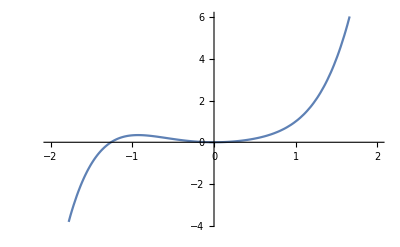

```mathematica
Plot[y[t]/.solex4,{t,-2,2}]
```

When you first give the solution a name, then you can plot it as usual.

```mathematica
solfuncex4=solex4⟦1,1,2⟧
```

Function[{t},1/3 (2 t^2+t^5)]

or in an other way, with the same result:

```mathematica
solfuncex4=y/.solex4⟦1⟧
```

Function[{t},1/3 (2 t^2+t^5)]

```mathematica
Plot[solfuncex4[t],{t,-2,2}]
```

-Graphics-

#### Question 4

Plot the solutions of the following problems:
(a)	y'-3y=E^(2t),y(0)=0
(b)	y'+t y=t^3,y(0)=0
(c)	y'+y Tan(t)=Sin(2t),y(0)=2

-3 y[t]+y'[t]==ⅇ^(2 t)

{{y→Function[{t},ⅇ^(2 t) (-1+ⅇ^t)]}}

Function[{t},ⅇ^(2 t) (-1+ⅇ^t)]

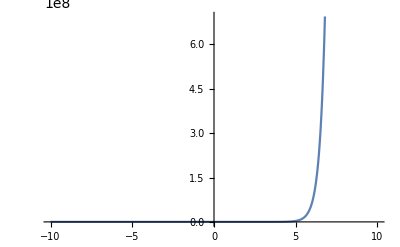

-Graphics-

t y[t]+y'[t]==t^3

{{y→Function[{t},ⅇ^(2 t) (-1+ⅇ^t)]}}

Function[{t},ⅇ^(2 t) (-1+ⅇ^t)]

ReplaceAll::reps: {-2.06274×10^-9} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-4.66618×10^-9} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-1.05554×10^-8} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
eq1= y'[t]-3 y[t]==E^(2t)
soleq1=DSolve[{eq1,y[0]==0},y,t]
solfunceq1=y/.soleq1⟦1⟧
Plot[solfunceq1[t],{t,-10,10}]
```

t y[t]+y'[t]==t^3

{{y→Function[{t},ⅇ^(-t^2/2) (2-2 ⅇ^(t^2/2)+ⅇ^(t^2/2) t^2)]}}

Function[{t},ⅇ^(-t^2/2) (2-2 ⅇ^(t^2/2)+ⅇ^(t^2/2) t^2)]

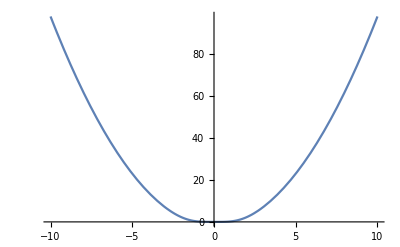

-Graphics-

Tan[t] y[t]+y'[t]==2 t Sin[t]

{{y→Function[{t},ⅇ^(-t^2/2) (4-2 ⅇ^(t^2/2)+ⅇ^(t^2/2) t^2)]}}

Function[{t},ⅇ^(-t^2/2) (2-2 ⅇ^(t^2/2)+ⅇ^(t^2/2) t^2)]

-Graphics-

```mathematica
eq2= y'[t]+t y[t]==t^3
soleq2=DSolve[{eq2,y[0]==0},y,t]
solfunceq2=y/.soleq2⟦1⟧
Plot[solfunceq2[t],{t,-10,10}]
```

Tan[t] y[t]+y'[t]==2 t Sin[t]

{{y→Function[{t},1/12 (24 Cos[t]+ⅈ π^2 Cos[t]+12 ⅈ t^2 Cos[t]-24 t Cos[t] Log[1+ⅇ^(2 ⅈ t)]+12 ⅈ Cos[t] PolyLog[2,-ⅇ^(2 ⅈ t)])]}}

Function[{t},1/12 (24 Cos[t]+ⅈ π^2 Cos[t]+12 ⅈ t^2 Cos[t]-24 t Cos[t] Log[1+ⅇ^(2 ⅈ t)]+12 ⅈ Cos[t] PolyLog[2,-ⅇ^(2 ⅈ t)])]

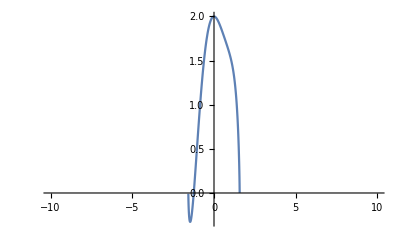

```mathematica
eq3= y'[t]+Tan[t] y[t]==Sin[t] 2t
soleq3=DSolve[{eq3,y[0]==2},y,t]
solfunceq3=y/.soleq3⟦1⟧
Plot[solfunceq3[t],{t,-10,10}]
```

### Plotting several solutions in one picture

It is easy to plot different solutions, for example with different initial values, in one figure. Using the "Table"-command you can make a list of functions, which can be plotted at once. In the next example we will use the equation of example 4.

#### Example 5

```mathematica
equex4=t y'[t]-2 y[t]==t^5
```

-2 y[t]+t y'[t]==t^5

```mathematica
solex5=DSolve[{equex4,y[1]==a},y,t]
```

{{y→Function[{t},1/3 (-t^2+3 a t^2+t^5)]}}

How can we plot a table of solution-functions, let us say for a = 0, 0.5, 1, 1.5, ..., 3 (7 solutions) and t going from -2 till 2? We could think of simply plotting the table:

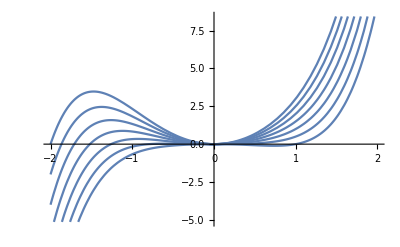

```mathematica
Plot[Table[y[t]/.solex5,{a,0,3,0.5}],{t,-2,2}]
```

Here Mathematica plots the complete table as one object. That's why all the graphs have the same color.
If we change the order, so that Mathematica first evaluates the table and then plots the graphs, then the solutions will be plotted as separate objects and will have different colors. This can be done by putting the command "Evaluate" between "Plot" and "Table". Now Mathematica will first evaluate the complete table of functions and then plot these functions.

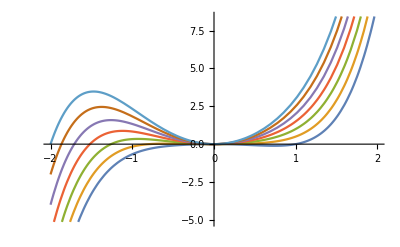

```mathematica
Plot[Evaluate[Table[y[t]/.solex5,{a,0,3,0.5}]],{t,-2,2}]
```

If we want to know what exactly are the formulas of the functions behind these 7 graphs, we ask for this table explicitly:

```mathematica
Table[y[t]/.solex5,{a,0,3,0.5}]
```

{{1/3 (0.-t^2+t^5)},{1/3 (0.5 t^2+t^5)},{1/3 (2. t^2+t^5)},{1/3 (3.5 t^2+t^5)},{1/3 (5. t^2+t^5)},{1/3 (6.5 t^2+t^5)},{1/3 (8. t^2+t^5)}}

#### Question 5

Do the same for one of the problems of question 4.

-a y[t]+y'[t]==ⅇ^(2 t)

{{y→Function[{t},(ⅇ^(-((-2+a) t)+a t) (-1+ⅇ^((-2+a) t)))/(-2+a)]}}

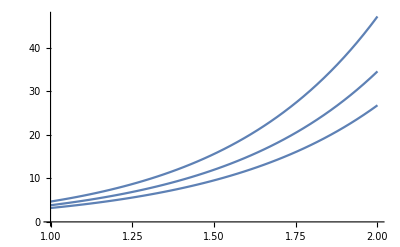

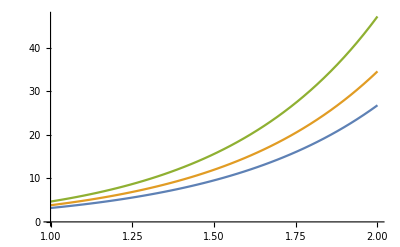

```mathematica
eq4= y'[t]-a y[t]==E^(2t)
soleq4=DSolve[{eq4,y[0]==0},y,t]
Plot[Table[y[t]/.soleq4,{a,0,1,0.5}],{t,1,2}]
Plot[Evaluate[Table[y[t]/.soleq4,{a,0,1,0.5}]],{t,1,2}]
```

### Direction field

Mathematica has a simple command for plotting the directionfield of differential equations or dynamic systems, namely VectorPlot.

```mathematica
?VectorPlot
```

Let us look again at an example.

```mathematica
y'[t]-2 t y[t]==t^2
```

-2 t y[t]+y'[t]==t^2

Now in the (t,y)-plane we can assign vectors representing the motion to an arbitrary point (t,y), namely (1,y')=(1,2t y+t^2). For example:

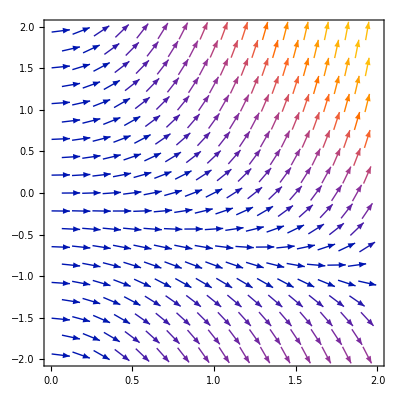

```mathematica
dirplot=VectorPlot[{1,2 t y+t^2},{t,0,2},{y,-2,2}]
```

The bigger the arrow, the higher the local speed of the motion.

Now it is possible to show particular solutions in the direction field. We first plot several solutions, for different initial values in one figure.

```mathematica
solut=DSolve[{y'[t]-2 t y[t]==t^2,y[0]==a},y,t]
```

{{y→Function[{t},1/4 (4 a ⅇ^(t^2)-2 t+ⅇ^(t^2) √π Erf[t])]}}

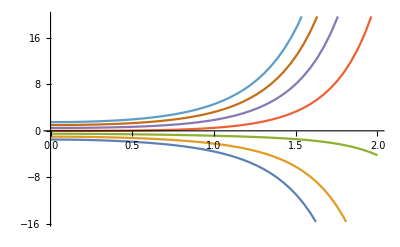

```mathematica
solplot=Plot[Evaluate[Table[y[t]/.solut,
	  {a,-1.5,1.5,0.5}]],{t,0,2}]
```

Now we show the solutions in the direction field.Mind to take the plotrange equal to the range of the direction field!

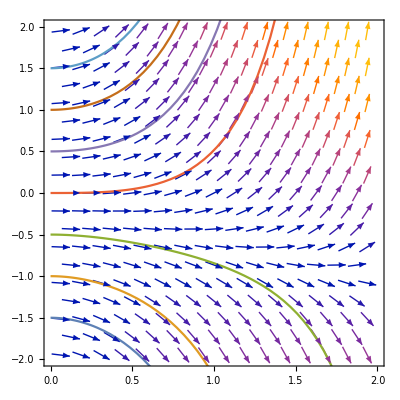

```mathematica
Show[{dirplot,solplot},PlotRange->{{0,2},{-2,2}}]
```

Coloring the solutions makes them just more visible.

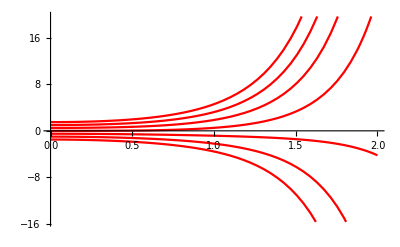

```mathematica
solplot=Plot[Evaluate[Table[y[t]/.solut,
           {a,-1.5,1.5,0.5}]],{t,0,2},
	       PlotStyle->RGBColor[1,0,0]]
```

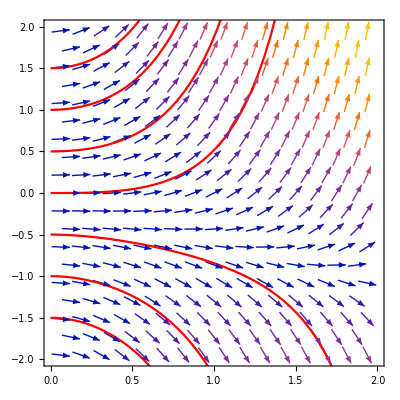

```mathematica
Show[{dirplot,solplot},PlotRange->{{0,2},{-2,2}},Axes->True]
```

### Using parameters

#### Example 6

We have already seen that Mathematica can solve differential equations with an initial value as parameter. Another example is the following. Look at the differential equation 
p'=a (b_1-c_1 p+b_2-c_2 p)

```mathematica
equex6:=p'[t]==a (b1-c1 p[t]+b2-c2 p[t])
```

Notice the delayed definition with the colon, which is always the most appropriate if parameters play a role.

```mathematica
solex6=DSolve[equex6,p,t]
```

{{p→Function[{t},((b1+b2) ⅇ^(-a c1 t-a c2 t+a (c1+c2) t))/(c1+c2)+ⅇ^(-a c1 t-a c2 t) C[1]]}}

```mathematica
solfuncex6=solex6⟦1,1,2⟧
```

Function[{t},((b1+b2) ⅇ^(-a c1 t-a c2 t+a (c1+c2) t))/(c1+c2)+ⅇ^(-a c1 t-a c2 t) C[1]]

Now parameters can be given values and the result can be used for further calculations.

```mathematica
a=1;c1=1;c2=2;
```

For example the longrun behavior of the solution can be evaluated:

```mathematica
Limit[solfuncex6[t],t->∞]
```

(b1+b2)/3

```mathematica
ClearAll[a,c1,c2]
```

#### Question 6

Take a = 1 and make a table of solutions of the equation in example 6 for different values of b_1,  b_2, c_1 and c_2. Also plot these solutions in one figure, taking p(0) = 1.

```mathematica
ClearAll[a,b1,b2,c1,c2]
a=1
```

```mathematica
soleq6=DSolve[{equex6,p[0]==1},p,t]
Plot[Table[y[t]/.soleq6,{b1=RandomInteger[1,100]},{b2=RandomInteger[1,100]},{c1=RandomInteger[1,100]},{c2=RandomInteger[1,100]}],{t,1,2}]
```

12

## Numerical solutions with NDSolve

### Limitations of DSolve

There are a lot of differential equations that cannot be solved with "DSolve". Especially linear differential equations of order higher than 4 and nonlinear differential equations generally cannot be handled using "DSolve". Nevertheless, as Mathematica develops, it can solve more and more differential equations exactly. For example the equation in example 7 could not be solved in Version 2 of Mathematica, but it can in Version 3 and up. the more complicated equation in example 8 cannot even be solved in version 6.

#### Example 7

```mathematica
equex7=(x y[x]+x^2) y'[x]+y[x]^2+3 x y[x]==0
```

3 x y[x]+y[x]^2+(x^2+x y[x]) y'[x]==0

```mathematica
solex7=DSolve[equex7,y,x]
```

{{y→Function[{x},-x-(√(ⅇ^(2 C[1])+x^4))/x]},{y→Function[{x},-x+(√(ⅇ^(2 C[1])+x^4))/x]}}

#### Example 8

```mathematica
equex8=y''[x]+√x y'[x]+y[x]/(ⅇ^(x^2))==0
```

ⅇ^(-x^2) y[x]+√x y'[x]+y''[x]==0

```mathematica
solex8=DSolve[equex8,y,x]
```

DSolve[ⅇ^(-x^2) y[x]+√x y'[x]+y''[x]==0,y,x]

The only thing you may do now is evaluating a numerical approximation to solutions. Mathematica has a built-in numerical differential equation solver, named "NDSolve".

### Solving

#### Example 9

We deal with the problem of example 8 with NDSolve. 
Because a solution is a numerical approximation, we should indicate what must be the domain of a solution, i.e. give a lower and an upper bound for the independent variable. Moreover, enough initial conditions are absolutely necessary, and no parameters may occur in the equations. The (numerical) approximation we find is not an explicit function, but some rule that will calculate for each value of time t the corresponding values of the dynamic variable(s). The only way to get an idea of the solution is to evaluate tables with function values and make plots.
Notice that the equation of example 8 is neither autonomous nor 1st order, although it is linear.

```mathematica
equex8=y''[x]+√x y'[x]+ⅇ^(-x^2) y[x]==0
```

ⅇ^(-x^2) y[x]+√x y'[x]+y''[x]==0

```mathematica
nsolex9=NDSolve[{equex8,y[0]==1,y'[0]==1},y,{x,0,10}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
funcnsol9=nsolex9⟦1,1,2⟧
```

InterpolatingFunction[…]

```mathematica
funcnsol9[3]
```

1.16452

#### Question 7

Make a table of solutions for the problem in example 9 with different initial conditions, for example with y(0)=m and y'(0)=n where m and n can have the values 0, 1, or 2.

```mathematica
nsolex9=NDSolve[{equex8,y[0]==m,y'[0]==n, {{m,0,2,1},{n,0,2,1}}},y,{x,0,10}]
Table[y[t]/.funcnsol9[x],{x,0,10}]
```

NDSolve::deqn: Equation or list of equations expected instead of m in the first argument {ⅇ^(-x^2) y[x]+√x y'[x]+y''[x]==0,y[0]==m,y'[0]==n,{{m,0,2,1},{n,0,2,1}}}.

NDSolve[{ⅇ^(-x^2) y[x]+√x y'[x]+y''[x]==0,y[0]==m,y'[0]==n,{{m,0,2,1},{n,0,2,1}}},y,{x,0,10}]

ReplaceAll::reps: {0[0]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0[1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0[2]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{y[t]/.0[0],y[t]/.0[1],y[t]/.0[2],y[t]/.0[3],y[t]/.0[4],y[t]/.0[5],y[t]/.0[6],y[t]/.0[7],y[t]/.0[8],y[t]/.0[9],y[t]/.0[10]}

### Plotting

#### Example 10

We plot the solution of example 9.

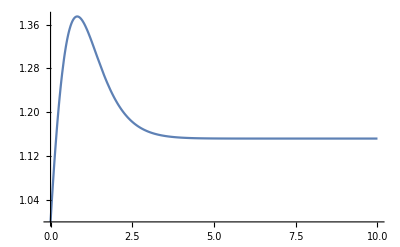

```mathematica
Plot[funcnsol9[t],{t,0,10}]
```

Again there is another way of plotting the solutions,omitting the stage of defining a solution function.

```mathematica
Plot[y[x]/.nsolex9,{x,0,10}]
```

-Graphics-

#### Question 8

Plot all solutions calculated in question 7 in one figure.

## Nonlinear FODE

## Solving

We have already seen some nonlinear differential equations in the subsection on the limitations of "DSolve". Here is another one.

#### Example 11

The differential equation
	x'=4 t^2 x^2
can be solved by hand because it is a so-called separable equation (x's and t's can be separated into x'/x^2=4 t^2).
Of course DSolve can solve this kind of equations.

```mathematica
equex11=DSolve[x'[t]==4 t^2 x[t]^2,x,t]
```

{{x→Function[{t},-3/(4 t^3+3 C[1])]}}

!!However the zero solution is not found!!.....an incompleteness of the package?!

#### Question 9

Solve the equation
	x[t] x'[t] == 1
and check for correctness.

```mathematica
eq9=x[t]x'[t]==1
```

x[t] x'[t]==1

```mathematica
soleq9=DSolve[x[t]x'[t]==1,x,t]
```

{{x→Function[{t},-√2 √(t+C[1])]},{x→Function[{t},√2 √(t+C[1])]}}

```mathematica
{{x->Function[{t},-√2 √(t+C[1])]},{x->Function[{t},√2 √(t+C[1])]}}
solfunceq9=soleq9⟦1,1,2⟧
eq9/.x->solfunceq9
```

{{x→Function[{t},-√2 √(t+C[1])]},{x→Function[{t},√2 √(t+C[1])]}}

Function[{t},-√2 √(t+C[1])]

True

#### Example 12

We reconsider the nonlinear FODE of example 7.

```mathematica
equex7=(x y[x]+x^2) y'[x]+y[x]^2+3 x y[x]==0
```

3 x y[x]+y[x]^2+(x^2+x y[x]) y'[x]==0

```mathematica
solex7=DSolve[equex7,y,x]
```

{{y→Function[{x},-x-(√(ⅇ^(2 C[1])+x^4))/x]},{y→Function[{x},-x+(√(ⅇ^(2 C[1])+x^4))/x]}}

Defining a solution function.

```mathematica
solfuncex7=solex7⟦1,1,2⟧
```

Function[{x},-x-(√(ⅇ^(2 C[1])+x^4))/x]

```mathematica
solfuncex7[r]
```

-r-(√(ⅇ^(2 C[1])+r^4))/r

Checking for correctness of the solutions.

```mathematica
Simplify[equex7/.solex7]
```

{True,True}

## Plotting

Plotting Nonlinear FODEs is similar to plotting linear FODEs.

## Higher Order Differential Equation (HODE)

To solve higher order differential equations you should follow exactly the same procedure as in the case of solving FODEs. However you should take into account that numerically solving HODEs requires more initial conditions than in the FODE-case.

#### Example 13

Consider the second order equation y''-2y'+y=0. The general solution can easily be found:

```mathematica
solex13=DSolve[y''[t]-2 y'[t]+y[t]==0,y,t]
```

{{y→Function[{t},ⅇ^t C[1]+ⅇ^t t C[2]]}}

And with initial conditions:

```mathematica
initsolex13=DSolve[{y''[t]-2 y'[t]+y[t]==0,y[0]==1,y'[0]==2},y,t]
```

{{y→Function[{t},ⅇ^t (1+t)]}}

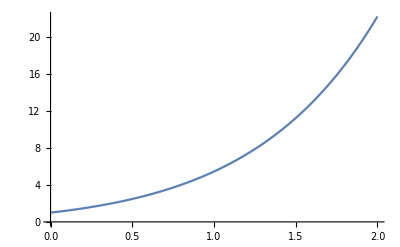

```mathematica
Plot[y[t]/.initsolex13,{t,0,2}]
```

#### Question 10

Try to solve the following differential equations, using Mathematica.
(a) 	y''' - y'' + y' - y = 0
(b)	y''' - 6y'' + 11y' - 6y = 0
(c)	y''' + 8y = 0

```mathematica
solex13=DSolve[y''[t]-2 y'[t]+y[t]==0,y,t]
```

{{y→Function[{t},ⅇ^t C[1]+ⅇ^t t C[2]]}}

```mathematica
soleq10=DSolve[y'''[t]-y''[t]+y'[t]-y[t]==0,y,t]
soleq11=DSolve[y'''[t]-6 y'[t]+11 y'[t]-6y[t]==0,y,t]
soleq12=DSolve[y'''[t]+8y[t]==0,y,t]
```

DSolve::dvnoarg: The function y appears with no arguments.

DSolve[-y[t]+y'''[t]+y'[t]-y''[t]==0,y[t],t]

DSolve::dvnoarg: The function y appears with no arguments.

DSolve[-6 y[t]+y'''[t]+5 y'[t]==0,y,t]

DSolve::dvnoarg: The function y appears with no arguments.

DSolve[8 y[t]+y'''[t]==0,y,t]

## The use of Manipulate for ODEs

### Solving

Consider a differential equation with some parameters in it. The following second order, linear, homogeneous equation has one coefficient as a parameter and both initial values. For the parameter values we only take integers.:

```mathematica
Manipulate[DSolve[{p''[t]==a p'[t]-p[t],p[0]==p0,p'[0]==p1},p,t],{a,-2,2,1},{p0,-2,2,1},{p1,-2,2,1}]
```

### Plotting

We plot the solution of the same equation. For the coefficient a we take a continuous range now. Again we need the Evaluate command to first solve the equation before plotting.

```mathematica
Manipulate[Plot[Evaluate[p[t]/.DSolve[{p''[t]==a p'[t]-p[t],p[0]==p0,p'[0]==p1},p,t]],{t,0,50}],{a,-2,2},{p0,-2,2,1},{p1,-2,2,1}]
```

Answers to the questions

Links to all notebooks

basicsDMDO
calc1 calc2 calc3 calc4 calc5
matrices
ode
odesys